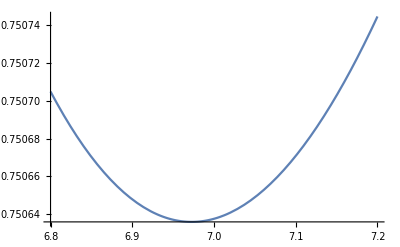

```mathematica
Plot[(2*Pi^2/(3*x^2))^(1/x),{x,6.8,7.2}]
```

```mathematica
.
```

```mathematica
f[x_]:=(2*Pi^2/(3*x^2))^(1/x)
```

```mathematica
FindMinimum[f[x],x]
```

{0.750636,{x→6.97266}}

```mathematica
0.75*6
```

4.5

```mathematica
b[m_,d_]:=Zeta[d-1]*(m/(d-1))^(1-d)
```

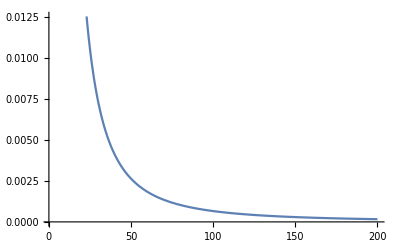

```mathematica
Plot[b[m,3],{m,1,200}]
```

```mathematica
g[m_,d_]:=b[m,d]^(1/m)
```

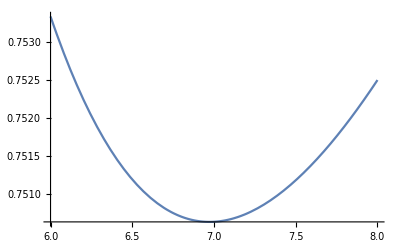

```mathematica
Plot[g[m,3],{m,6,8}]
```

```mathematica
FindMinimum[g[m,3],m]
```

{0.750636,{m→6.97266}}

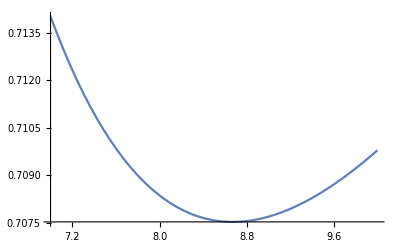

```mathematica
Plot[g[m,4],{m,7,10}]
```

```mathematica
FindMinimum[g[m,4],m]
```

{0.707519,{m→8.67076}}

```mathematica
FindMinimum[g[m,5],m]
```

{0.697205,{m→11.0903}}

```mathematica
N[Zeta[10]]
```

1.00099

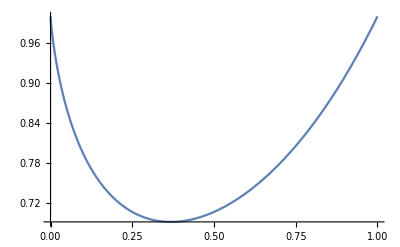

```mathematica
Plot[x^x,{x,0,1}]
```

```mathematica
FindMinimum[x^x,x]
```

{0.692201,{x→0.367879}}

```mathematica
h[m_,d_]:=(m/(d-1))^((1-d)/m)*2d
```

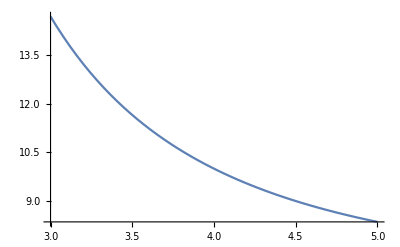

```mathematica
Plot[h[m,5],{m,3,5}]
```

```mathematica
H[k_,i_]:= Binomial[k,i]*(1/i)(1/(k-i))
```

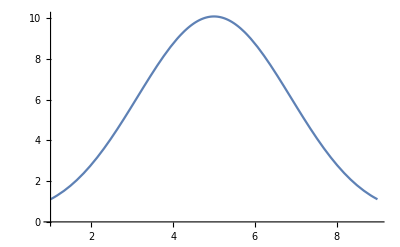

```mathematica
Plot[H[10,i],{i,1,9}]
```